## Appendix A7 (Allee effect)

### Setup

```mathematica
ClearAll["α","β","f"]
```

```mathematica
f[ν_,σ_,ζ_]:=ν NIntegrate[Exp[-x^2/σ^2]Exp[(-(x-ζ)^4)/(81 σ^4)],{x,-Infinity,Infinity}]/NIntegrate[Exp[-x^2/σ^2]^2,{x,-Infinity,Infinity}]
```

#### Dynamics

```mathematica
Subscript[dN, 1]:=Subscript[N, 1](1-S^4/ω^4-(β Subscript[N, 1]+α Subscript[N, 2]));
Subscript[dN, 2]:=Subscript[N, 2](1-(S-ϵ)^4/ω^4-(α Subscript[N, 1]+β Subscript[N, 2]));
dS:=η(-S)Subscript[N, 1]+η(ϵ-S)Subscript[N, 2];
```

```mathematica
Jc:={{D[Subscript[dN, 1],Subscript[N, 1]],D[Subscript[dN, 1],Subscript[N, 2]],D[Subscript[dN, 1],S]},{D[Subscript[dN, 2],Subscript[N, 1]],D[Subscript[dN, 2],Subscript[N, 2]],D[Subscript[dN, 2],S]},{D[dS,Subscript[N, 1]],D[dS,Subscript[N, 2]],D[dS,S]}};
```

#### Equilibrium

```mathematica
eqN=FullSimplify[Solve[Subscript[dN, 1]==0&&Subscript[dN, 2]==0,{Subscript[N, 1],Subscript[N, 2]}]]
```

{{N_1→0,N_2→0},{N_1→0,N_2→(-(S-ϵ)^4+ω^4)/(β ω^4)},{N_1→(1+(S^4 (-α+β)+4 S^3 α ϵ-6 S^2 α ϵ^2+4 S α ϵ^3-α ϵ^4)/((α-β) ω^4))/(α+β),N_2→(1+(S^4 (-α+β)-4 S^3 β ϵ+6 S^2 β ϵ^2-4 S β ϵ^3+β ϵ^4)/((α-β) ω^4))/(α+β)},{N_1→(1-S^4/ω^4)/β,N_2→0}}

### Figure A7a (PSF and competition - allee effect, coexistence only when initial population is large)

```mathematica
pars={ω->1,σ->1,ν->1,η->1,ζ->2,ϵ->0.8};
α=f[ν/.pars,σ/.pars,ζ/.pars]
β=f[ν/.pars,σ/.pars,0]
```

1.06713

1.40176

```mathematica
ys=Range[0,1,0.005];
ny=Length[ys];
```

```mathematica
ClearAll["xf","yf","zf"]
```

```mathematica
xf=Array[,ny];
yf=Array[,ny];
zf=Array[,ny];
```

```mathematica
T=1000; 
dx=Subscript[dN, 1]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dy=Subscript[dN, 2]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dz=dS/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
```

This defines Dormand and Prince coefficients to solve ODE equivalently to ode45 in MATLAB

```mathematica
DOPRIamat={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DOPRIbvec={35/384,0,500/1113,125/192,-2187/6784,11/84,0};
DOPRIcvec={1/5,3/10,4/5,8/9,1,1};
DOPRIevec={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};
DOPRICoefficients[5,p_]:=N[{DOPRIamat,DOPRIbvec,DOPRIcvec,DOPRIevec},p];
```

```mathematica
Timing[
Do[
nsol=NDSolve[{D[x[t],t]==dx,D[y[t],t]==dy,D[z[t],t]==dz,x[0]==1/β,y[0]==ys[[j]],z[0]==0},{x,y,z},{t,0,T},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
xf[[j]]=Flatten[{ys[[j]],x[T]/.nsol}];
yf[[j]]=Flatten[{ys[[j]],y[T]/.nsol}];
zf[[j]]=Flatten[{ys[[j]],z[T]/.nsol}],
{j,ny}]
]
```

{0.5,Null}

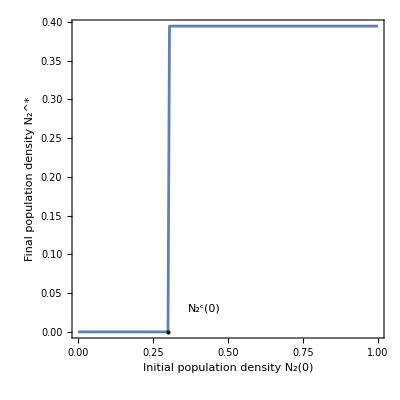

```mathematica
figA7a=ListLinePlot[yf,Frame->True,FrameLabel->{"Initial population density N_2(0)","Final population density N_2^*"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},AspectRatio->1,Epilog-> {{PointSize[Large],Point[{0.3,0}]},{Inset[Text[Style["N_2^c(0)",FontSize->20]],{0.42,0.03}]}}]
```

```mathematica
Export["\\\\wsl.localhost\\Ubuntu\\home\\athma\\trait_cond_models\\paper_2\\images\\figA7a.pdf",figA7a];
```

### Figure A7b (Allee effect - how does dissimilarity affect the allee threshold)

```mathematica
ClearAll["xf","yf","zf","pars"]
```

```mathematica
pars={ω->1,σ->1,ν->1,η->1,ζ->2};
α=f[ν/.pars,σ/.pars,ζ/.pars]
β=f[ν/.pars,σ/.pars,0]
```

1.06713

1.40176

```mathematica
ϵs=Range[0.65,0.9,0.005];
nϵ=Length[ϵs];
ys=Range[0,3,0.01];
ny=Length[ys];
```

```mathematica
yf=Array[,nϵ];
```

```mathematica
T=1000; 
dx=Subscript[dN, 1]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dy=Subscript[dN, 2]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dz=dS/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
```

```mathematica
Timing[
checkN=0;
j1=1;
While[checkN==0&&j1<=nϵ,
check=0;
j2=1;
While[check==0&&j2<=ny,
nsol=NDSolve[{D[x[t],t]==(dx/.ϵ->ϵs[[j1]]),D[y[t],t]==(dy/.ϵ->ϵs[[j1]]),D[z[t],t]==(dz/.ϵ->ϵs[[j1]]),x[0]==1/β,y[0]==ys[[j2]],z[0]==0},{x,y,z},{t,0,T},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
If[check==0&&Extract[y[T]/.nsol,1]>0.1&&Extract[x[T]/.nsol,1]>0.1,yf[[j1]]={ϵs[[j1]],ys[[j2]]};check=1];
j2=j2+1
];
If[check==0,checkN=1;ϵNul=ϵs[[j1]];yMax=yf[[j1-1,2]]];
j1=j1+1
]
]
```

{3.32813,Null}

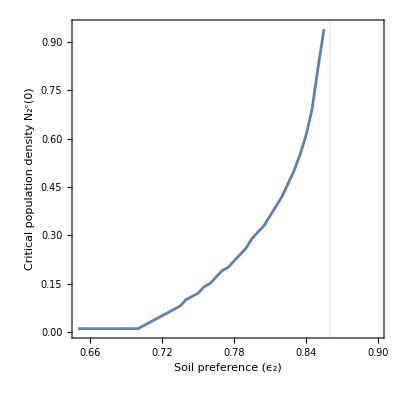

```mathematica
figA7b=ListLinePlot[yf,Frame->True,FrameLabel->{"Soil preference (ϵ_2)","Critical population density N_2^c(0)"},Axes->{False,False},LabelStyle->{FontSize->20,FontColor->Black},PlotRange->{{0.65,0.9},{0,1.01yMax}},GridLines->{{ϵNul},{}},AspectRatio->1]
```

```mathematica
Export["\\\\wsl.localhost\\Ubuntu\\home\\athma\\trait_cond_models\\paper_2\\images\\figA7b.pdf",figA7b];
```

### Numerics

```mathematica
pars={ω->1,σ->1,ν->1,η->1,ζ->2,ϵ->0.8};
α=f[ν/.pars,σ/.pars,ζ/.pars]
β=f[ν/.pars,σ/.pars,0]
```

1.06713

1.40176

```mathematica
T=1000; 
dx=Subscript[dN, 1]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dy=Subscript[dN, 2]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dz=dS/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
```

```mathematica
nsol=NDSolve[{D[x[t],t]==dx,D[y[t],t]==dy,D[z[t],t]==dz,x[0]==1/β,y[0]==0.35,z[0]==0},{x,y,z},{t,0,T},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
```

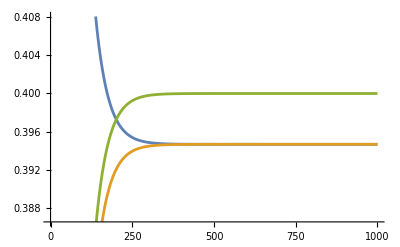

```mathematica
Plot[{x[t]/.nsol,y[t]/.nsol,z[t]/.nsol},{t,0,T}]
```

```mathematica
{Extract[x[T]/.nsol,1],Extract[y[T]/.nsol,1]}
```

{0.39467,0.39467}